{a→0.154961,b→0.477731,c→-0.00984387}

0.998958

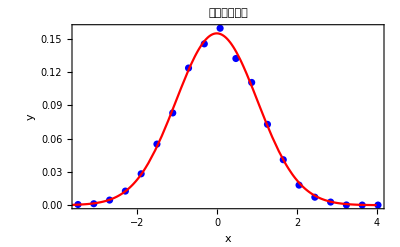

```mathematica
(*输入观测数据*)data={{-3.49168,0.0006},{-3.09553,0.0013},{-2.69937,0.0046},{-2.30322,0.0127},{-1.90707,0.0283},{-1.51091,0.0551},{-1.11476,0.0832},{-0.718608,0.1237},{-0.322455,0.1455},{0.0736986,0.1596},{0.469852,0.1323},{0.866005,0.1107},{1.26216,0.0729},{1.65831,0.041},{2.05446,0.0181},{2.45062,0.0072},{2.84677,0.0028},{3.24292,0.0002},{3.63908,0.0001},{4.03523,0.0001}};

(*定义高斯函数模型*)
model=a Exp[-b (x-c)^2];

(*非线性拟合*)
fit=NonlinearModelFit[data,model,{a,b,c},x];

(*输出拟合参数*)
fit["BestFitParameters"]
(*输出:{a->,b->,c->}*)

(*计算R.b2*)
fit["RSquared"]
(*输出:R.b2*)

(*绘制原始数据与拟合曲线*)
Show[ListPlot[data,PlotStyle->Blue,PlotLabel->"高斯拟合结果"],Plot[fit[x],{x,-4,4},PlotStyle->Red],Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Placed[{"原始数据","拟合曲线"},Top]]
```